# Modelo CAM

```mathematica
chooseLeague = "La Lga";
```

## Importing data

```mathematica
If[chooseLeague=="La Liga",
	dfList = Import["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligaespana.csv"],
	dfList = Import["C:/Users/geral/OneDrive - Universidad del Pacífico/Trabajos/CMA/data_ligainglesa_completo.csv"]
	];
dfAssociation=AssociationThread[dfList[[1]]->#]&/@Rest[dfList];
dfDataSet=Dataset[dfAssociation];
dfDataSet=dfDataSet[All,Append[#,"Total"->(#FTHG+#FTAG)]&];
dfDataSet=dfDataSet[All,Append[#,"Difference"->(Abs[#FTHG-#FTAG])]&];
```

## Variable construction

### ELO rating construction

```mathematica
(* Inicializar parámetros ELO *)
initialElo = 1500;
kFactor = 10;

(* Función para calcular la puntuación esperada *)
expectedScore[ratingA_, ratingB_] := 1/(1 + 10^((ratingB - ratingA)/400));

(* Función para actualizar la calificación ELO *)
updateElo[currentRating_, expected_, actual_] := currentRating + kFactor * (actual - expected);

(* Inicializar diccionario de calificaciones ELO *)
eloRatings = <||>;

(* Procesar cada partido para actualizar las calificaciones ELO *)
dfDataSet[All, 
  Function[match, 
   Module[{homeTeam, awayTeam, homeGoals, awayGoals, homeRating, 
     awayRating, homeExpected, awayExpected, homeActual, awayActual},
    
    homeTeam = match["HomeTeam"];
    awayTeam = match["AwayTeam"];
    homeGoals = match["FTHG"];
    awayGoals = match["FTAG"];
    
    (* Inicializar calificaciones ELO si los equipos no están calificados *)
    If[! KeyExistsQ[eloRatings, homeTeam], 
     eloRatings[homeTeam] = initialElo];
    If[! KeyExistsQ[eloRatings, awayTeam], 
     eloRatings[awayTeam] = initialElo];
    
    (* Obtener calificaciones actuales *)
    homeRating = eloRatings[homeTeam];
    awayRating = eloRatings[awayTeam];
    
    (* Calcular puntuaciones esperadas *)
    homeExpected = expectedScore[homeRating, awayRating];
    awayExpected = expectedScore[awayRating, homeRating];
    
    (* Determinar puntuaciones reales basadas en el resultado del partido *)
    Which[
     homeGoals > awayGoals, homeActual = 1; awayActual = 0;,
     homeGoals < awayGoals, homeActual = 0; awayActual = 1;,
     True, homeActual = 0.5; awayActual = 0.5
     ];
    
    (* Actualizar calificaciones *)
    eloRatings[homeTeam] = 
     updateElo[homeRating, homeExpected, homeActual];
    eloRatings[awayTeam] = 
     updateElo[awayRating, awayExpected, awayActual];
    ]
   ]];

(* Convertir las calificaciones ELO finales a una lista y ordenarlas por calificación *)
finalEloRatings = SortBy[Normal[eloRatings], -Last[#] &];

(* Mostrar las calificaciones ELO finales *)
 finalEloRatingsAssociation = finalEloRatings//Association;
```

### xG score construction

#### Season-weighted average goals (IMPROVE THIS PLEASE)

```mathematica
(* Paso 1: Convertir las fechas en objetos DateObject 
fechasConvertidas = DateObject[{ToExpression[StringTake[#, {7, 10}]], 
                                ToExpression[StringTake[#, {4, 5}]], 
                                ToExpression[StringTake[#, {1, 2}]]}] & /@ (dfDataSet[All,"Date"] // Normal);

(* Paso 2: Calcular la diferencia de días respecto al partido más reciente *)
diasDiferencia = DateDifference[#, Max[fechasConvertidas], "Month"] & /@ fechasConvertidas;

(* Extraer los valores numéricos de las diferencias de días *)
diasDiferenciaNumerico = diasDiferencia[[All, 1]];

(* Paso 3: Calcular los pesos usando una función exponencial inversa *)
pesos = Exp[-diasDiferenciaNumerico]; (* Esto dará más peso a los partidos recientes *)
pesosList = Prepend[pesos,"Weights"];

(* Paso 4: Extraer los goles de los equipos locales y visitantes *)
dfList = MapThread[Append,{dfList,pesosList}];
dfListxGHomeTeam = Rest[dfList[[All, {4, 6,-1}]]]; (* HomeTeam, FTHG *)
dfListxGAwayTeam = Rest[dfList[[All, {5, 7,-1}]]]; (* AwayTeam, FTAG *)

dfListxGHomeTeamWeighted = (Append[#, #[[2]] * #[[3]]] & /@ dfListxGHomeTeam); (*goles*peso*)
dfListxGAwayTeamWeighted = (Append[#, #[[2]] * #[[3]]] & /@ dfListxGAwayTeam); (*goles*peso*)

weightedAverageHomeTeamAssociation = GroupBy[dfListxGHomeTeamWeighted, First -> Last,Function[x,Total[x]]]/Total[pesos];*)
```

#### Average goals (MEANWHILE WE USE THIS)

```mathematica
(* Paso 1: Extraer los goles de los equipos locales y visitantes con sus respectivos equipos *)
dfListxGHomeTeam = Rest[dfList[[All, {4, 6}]]]; (* HomeTeam, FTHG *)
dfListxGAwayTeam = Rest[dfList[[All, {5, 7}]]]; (* AwayTeam, FTAG *)

(* Paso 2: Combinar las listas de equipos y goles *)
combinedGoalsList = Join[
   dfListxGHomeTeam,
   dfListxGAwayTeam
   ];

(* Paso 3: Calcular el promedio de goles por equipo, sin diferenciar entre local y visita *)
averageGoalsAssociation = GroupBy[combinedGoalsList, First -> Last, Mean];
averageGoalsHomeTeamAssociation = GroupBy[dfListxGHomeTeam, First -> Last, Mean];
averageGoalsAwayTeamAssociation = GroupBy[dfListxGAwayTeam, First -> Last, Mean];
```

### Other variables average construction

```mathematica
(*

(* Extraer disparos totales para el equipo local y visitante *)
dfListShotsHomeTeam = Rest[dfList[[All, {4, 13}]]]; (* HomeTeam, Shots *)
dfListShotsAwayTeam = Rest[dfList[[All, {5, 14}]]]; (* AwayTeam, Shots *)

(* Extraer disparos al arco para el equipo local y visitante *)
dfListShotsTargetHomeTeam = Rest[dfList[[All, {4, 15}]]]; (* HomeTeam, Shots on Target *)
dfListShotsTargetAwayTeam = Rest[dfList[[All, {5, 16}]]]; (* AwayTeam, Shots on Target *)

(* Calcular la proporción de disparos que van al arco para el equipo local *)
proportionShotsOnTargetHomeTeam = 
  MapThread[{#1, #2/#3} &, 
    {dfListShotsHomeTeam[[All, 1]], 
     dfListShotsTargetHomeTeam[[All, 2]], 
     dfListShotsHomeTeam[[All, 2]]}
  ];

(* Calcular la proporción de disparos que van al arco para el equipo visitante *)
proportionShotsOnTargetAwayTeam = 
  MapThread[{#1, #2/#3} &, 
    {dfListShotsAwayTeam[[All, 1]], 
     dfListShotsTargetAwayTeam[[All, 2]], 
     dfListShotsAwayTeam[[All, 2]]}
  ];

(* Combinar *)
combinedShotsProportionList = Join[
   proportionShotsOnTargetAwayTeam,
   proportionShotsOnTargetHomeTeam
   ];
averageShotsProportionAssociation = N[GroupBy[combinedShotsProportionList, First -> Last, Mean]];
*)
```

## Model Building

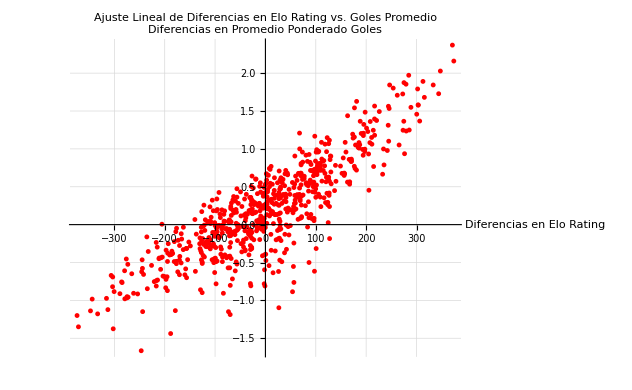

```mathematica
(* Obtener la lista de equipos *)
teams = Keys[finalEloRatingsAssociation];

(* Crear una lista vacía para almacenar las diferencias *)
differences = {};

(* Calcular las diferencias en promedio ponderado de goles y Elo ratings para cada par de equipos *)
Do[
  Do[
    If[team1 != team2,
      AppendTo[
        differences, 
        {
          finalEloRatingsAssociation[team1] - finalEloRatingsAssociation[team2],
          averageGoalsHomeTeamAssociation[team1] - averageGoalsAwayTeamAssociation[team2],
          team1,
          team2
        }
      ]
    ],
    {team2, teams}
  ],
  {team1, teams}
];

(* Extraer las diferencias de Elo y de goles *)
eloDifferences = differences[[All, 1]];
goalDifferences = differences[[All, 2]];
teamPairs = differences[[All, 3 ;; 4]]; (* Los nombres de los equipos también se almacenan *)

(* Realizar el ajuste lineal en las diferencias *)
modelFit = Fit[Transpose[{eloDifferences, goalDifferences}], {1, x}, x];

(* Graficar los puntos de datos y el ajuste lineal *)
Show[
  ListPlot[Transpose[{eloDifferences, goalDifferences}], PlotStyle -> Red, 
   AxesLabel -> {"Diferencias en Elo Rating", "Diferencias en Promedio Ponderado Goles"}, 
   PlotLabel -> "Ajuste Lineal de Diferencias en Elo Rating vs. Goles Promedio", 
   GridLines -> Automatic]
  (*Plot[modelFit, {x, Min[eloDifferences], Max[eloDifferences]}, PlotStyle -> Blue]*)
]

(* Calcular los valores predichos basados en el ajuste lineal *)
predictedValues = modelFit /. x -> # & /@ eloDifferences;

(* Crear un dataset con las predicciones, sin necesidad de teamsPairs explícitos *)
predictionsDatasetWithGoals = 
  Dataset[
    Table[
      Module[{team1 = teamPairs[[i, 1]], team2 = teamPairs[[i, 2]]},
        <|
          "Team Pair" -> {team1, team2},
          "Elo Difference" -> eloDifferences[[i]],
          "Predicted Goal Difference" -> predictedValues[[i]],
          "Home Team Weighted Goals" -> averageGoalsHomeTeamAssociation[team1],
          "Away Team Weighted Goals" -> averageGoalsAwayTeamAssociation[team2]
        |>
      ],
      {i, Length[eloDifferences]}
    ]
  ];

(* Ajustar los goles ponderados para que coincidan con la diferencia de goles predicha basada en el Elo rating *)
adjustedGoalsDataset = 
  Dataset[
    Table[
      Module[{team1 = teamPairs[[i, 1]], team2 = teamPairs[[i, 2]], 
              originalHomeGoals, originalAwayGoals, totalGoals, 
              predictedDifference, adjustedHomeGoals, adjustedAwayGoals,
              homeEloRating, awayEloRating, eloDifference},

        (* Goles ponderados originales *)
        (*
        originalHomeGoals = averageGoalsTestAssociation[team1];
        originalAwayGoals = averageGoalsTestAssociation[team2];
        *)
        originalHomeGoals = averageGoalsHomeTeamAssociation[team1];
        originalAwayGoals = averageGoalsAwayTeamAssociation[team2];
        
        (* Diferencia de goles predicha *)
        predictedDifference = predictedValues[[i]];

        (* Mantener los goles totales constantes *)
        totalGoals = originalHomeGoals + originalAwayGoals;

        (* Ajustar los goles del equipo local y visitante *)
        adjustedHomeGoals = (totalGoals + predictedDifference) / 2;
        adjustedAwayGoals = (totalGoals - predictedDifference) / 2;

        (* Ratings Elo *)
        homeEloRating = finalEloRatingsAssociation[team1];
        awayEloRating = finalEloRatingsAssociation[team2];
        eloDifference = homeEloRating - awayEloRating;

        <|
          "Team Pair" -> {team1, team2},
          "Home Elo Rating" -> homeEloRating,
          "Away Elo Rating" -> awayEloRating,
          "Elo Difference" -> eloDifference,
          "Original Home Goals" -> originalHomeGoals,
          "Original Away Goals" -> originalAwayGoals,
          "Predicted Goal Difference" -> predictedDifference,
          "Adjusted Home Goals" -> adjustedHomeGoals,
          "Adjusted Away Goals" -> adjustedAwayGoals
        |>
      ],
      {i, Length[eloDifferences]}
    ]
  ];
```

## Results

```mathematica
(* Definir los nombres del equipo local y visitante *)
localTeam = "Wolves";
awayTeam = "Newcastle";
nsim = 100000;

(* Extraer los goles ajustados para el equipo local y visitante basados en el modelo *)
adjustedGoalsLocal = adjustedGoalsDataset[
    Select[#["Team Pair"] == {localTeam, awayTeam} &], 
    "Adjusted Home Goals"
  ][[1]];
adjustedGoalsAway = adjustedGoalsDataset[
    Select[#["Team Pair"] == {localTeam, awayTeam} &], 
    "Adjusted Away Goals"
  ][[1]];

(* Simular partidos *)
simulatedMatches = 
  Table[
    <|
      localTeam <> " Goals" -> RandomVariate[PoissonDistribution[adjustedGoalsLocal//Normal]],
      awayTeam <> " Goals" -> RandomVariate[PoissonDistribution[adjustedGoalsAway//Normal]]
    |>,
    {nsim}
  ];
```

```mathematica
(* Definir las variables de la apuesta combinada *)
totalGoalsLowerBound = 0.5; (* Por ejemplo, al menos 1 gol *)
totalGoalsUpperBound = 4.5; (* Por ejemplo, como máximo 6 goles *)
handicapCombinada = 2.0; (* Handicap aplicado, puede ser local o visitante *)
handicapTeam = "away"; (* Puede ser "local" o "away" *)
ganaEmpataTeam = "local"; (* Puede ser "local" o "away" *)
cuotaCombinada = 1.42;

(* Calcular la probabilidad de victoria, derrota y empate del equipo local *)
wins = Count[simulatedMatches, _?(#[(localTeam <> " Goals")] > #[(awayTeam <> " Goals")] &)];
draws = Count[simulatedMatches, _?(#[(localTeam <> " Goals")] == #[(awayTeam <> " Goals")] &)];
losses = Count[simulatedMatches, _?(#[(localTeam <> " Goals")] < #[(awayTeam <> " Goals")] &)];

(* Calcular las probabilidades *)
totalMatches = Length[simulatedMatches];
winProbability = wins/totalMatches;
drawProbability = draws/totalMatches;
lossProbability = losses/totalMatches;

(* Crear tabla con las probabilidades de victoria, derrota y empate del equipo local *)
probabilidadesLocal = Dataset[{
  <|"Resultado" -> "Victoria " <> localTeam, "Probabilidad" -> winProbability|>,
  <|"Resultado" -> "Empate " <> localTeam, "Probabilidad" -> drawProbability|>,
  <|"Resultado" -> "Derrota " <> localTeam, "Probabilidad" -> lossProbability|>
}]

(* Determinar el equipo al que se aplica el handicap normal *)
teamGoalsForHandicapCombinada = 
  If[handicapTeam == "local", localTeam <> " Goals", awayTeam <> " Goals"];
otherTeamGoalsForHandicapCombinada = 
  If[handicapTeam == "local", awayTeam <> " Goals", localTeam <> " Goals"];

(* Determinar el equipo al que se aplica la condición "Gana o Empata" *)
teamGoalsForGanaEmpata = 
  If[ganaEmpataTeam == "local", localTeam <> " Goals", awayTeam <> " Goals"];
otherTeamGoalsForGanaEmpata = 
  If[ganaEmpataTeam == "local", awayTeam <> " Goals", localTeam <> " Goals"];

(* Evaluar cada criterio individualmente para la combinada *)
criterioHandicap = Count[
    simulatedMatches,
    _?(#[teamGoalsForHandicapCombinada] - #[otherTeamGoalsForHandicapCombinada] > -handicapCombinada &)
  ];

criterioTotalGolesLower = Count[
    simulatedMatches,
    _?(#[(localTeam <> " Goals")] + #[(awayTeam <> " Goals")] >= totalGoalsLowerBound &)
  ];

criterioTotalGolesUpper = Count[
    simulatedMatches,
    _?(#[(localTeam <> " Goals")] + #[(awayTeam <> " Goals")] <= totalGoalsUpperBound &)
  ];

criterioGanaEmpata = Count[
    simulatedMatches,
    _?(#[teamGoalsForGanaEmpata] >= #[otherTeamGoalsForGanaEmpata] &)
  ];
  
criterioAA = Count[
    simulatedMatches,
    _?(#[localTeam <> " Goals"] > 0 &&  #[awayTeam <> " Goals"] > 0 &)
  ];

(* Evaluar la probabilidad de éxito de la combinada completa *)
combinadaExito = 
  Count[
    simulatedMatches,
    _?(#[teamGoalsForHandicapCombinada] - #[otherTeamGoalsForHandicapCombinada] > -handicapCombinada && 
        #[(localTeam <> " Goals")] + #[(awayTeam <> " Goals")] > totalGoalsLowerBound &&
        #[(localTeam <> " Goals")] + #[(awayTeam <> " Goals")] < totalGoalsUpperBound &
        (*#[teamGoalsForGanaEmpata] >= #[otherTeamGoalsForGanaEmpata] &*)
        (*#[localTeam <> " Goals"] > 0 &&  (* Verificar que el equipo local haya anotado *)
        #[awayTeam <> " Goals"] > 0 &   (* Verificar que el equipo visitante haya anotado *)*)

    )
  ];

(* Calcular las probabilidades *)
probabilidadHandicap = criterioHandicap/nsim // N;
probabilidadTotalGolesLower = criterioTotalGolesLower/nsim // N;
probabilidadTotalGolesUpper = criterioTotalGolesUpper/nsim // N;
probabilidadGanaEmpata = criterioGanaEmpata/nsim // N;
probabilidadAA = criterioAA/nsim // N;
probabilidadExitoCombinada = combinadaExito/nsim // N;


(* Calcular el valor esperado para la combinada *)
valorEsperadoCombinada = (probabilidadExitoCombinada * cuotaCombinada) - (1 - probabilidadExitoCombinada);

(* Crear tabla con los resultados de la combinada *)
resultadosCombinada = Dataset[{
  <|"Criterio" -> "Handicap (" <> If[handicapTeam == "local", localTeam, awayTeam] <> " " <> ToString[handicapCombinada] <> ")", "Probabilidad" -> probabilidadHandicap|>,
  <|"Criterio" -> "Total Goles >" <> ToString[totalGoalsLowerBound], "Probabilidad" -> probabilidadTotalGolesLower|>,
  <|"Criterio" -> "Total Goles <" <> ToString[totalGoalsUpperBound], "Probabilidad" -> probabilidadTotalGolesUpper|>,
  <|"Criterio" -> "Gana o Empata " <> If[ganaEmpataTeam == "local", localTeam, awayTeam], "Probabilidad" -> probabilidadGanaEmpata|>,
  <|"Criterio" -> "Probabilidad AA", "Probabilidad" -> probabilidadAA|>,
  <|"Criterio" -> "Probabilidad Éxito Combinada", "Probabilidad" -> probabilidadExitoCombinada|>,
  <|"Criterio" -> "Valor Esperado", "Valor" -> valorEsperadoCombinada|>
}]
```

```mathematica
(* Definir diferentes líneas de handicap asiático para probar *)
handicaps = Range[-3.0, 3.0, 0.25];
cuotasListLocal = ConstantArray[1.4, Length[handicaps]]; (* Cuotas para el equipo local *)
cuotasListAway = ConstantArray[1.4, Length[handicaps]];  (* Cuotas para el equipo visitante *)
(*
cuotasListAway = Flatten[{ConstantArray[1.51, 15],1.675, 1.475, 1.375, 1.325, 1.220, 1.130, ConstantArray[1.51, 4]}];
*)

(* Calcular resultados de apuestas con cada handicap para ambos equipos *)
calculateResults[handicapAsianTeam_, cuotasList_] :=
  Module[{teamGoalsForHandicap, otherTeamGoalsForHandicap, results, EVResults},
    
    (* Seleccionar el equipo para el handicap asiático *)
    teamGoalsForHandicap = If[handicapAsianTeam == "local", localTeam <> " Goals", awayTeam <> " Goals"];
    otherTeamGoalsForHandicap = If[handicapAsianTeam == "local", awayTeam <> " Goals", localTeam <> " Goals"];
    
    (* Calcular resultados de apuestas con cada handicap *)
    results = 
      Table[
        Module[{handicap = hcap, winBet, pushBet, loseBet, totalBet, halfHandicap},
          
          (* Si el hándicap es de cuartos, dividir en dos apuestas *)
          If[FractionalPart[Abs[handicap]] == 0.25 || FractionalPart[Abs[handicap]] == 0.75,
            halfHandicap = {handicap + 0.25, handicap - 0.25};
            
            (* Evaluar la diferencia de goles en cada simulación para ambas partes del hándicap *)
            winBet = 
              Count[simulatedMatches, 
                _?(#[teamGoalsForHandicap] - #[otherTeamGoalsForHandicap] + halfHandicap[[1]] > 0 &)] +
              Count[simulatedMatches, 
                _?(#[teamGoalsForHandicap] - #[otherTeamGoalsForHandicap] + halfHandicap[[2]] > 0 &)];
                
            pushBet = 
              Count[simulatedMatches, 
                _?(#[teamGoalsForHandicap] - #[otherTeamGoalsForHandicap] + halfHandicap[[1]] == 0 &)] +
              Count[simulatedMatches, 
                _?(#[teamGoalsForHandicap] - #[otherTeamGoalsForHandicap] + halfHandicap[[2]] == 0 &)];
                
            loseBet = 
              Count[simulatedMatches, 
                _?(#[teamGoalsForHandicap] - #[otherTeamGoalsForHandicap] + halfHandicap[[1]] < 0 &)] +
              Count[simulatedMatches, 
                _?(#[teamGoalsForHandicap] - #[otherTeamGoalsForHandicap] + halfHandicap[[2]] < 0 &)];
            ,
            (* Si no es de cuartos, manejar como antes *)
            winBet = Count[simulatedMatches, 
              _?(#[teamGoalsForHandicap] - #[otherTeamGoalsForHandicap] + handicap > 0 &)];
            pushBet = Count[simulatedMatches, 
              _?(#[teamGoalsForHandicap] - #[otherTeamGoalsForHandicap] + handicap == 0 &)];
            loseBet = Count[simulatedMatches, 
              _?(#[teamGoalsForHandicap] - #[otherTeamGoalsForHandicap] + handicap < 0 &)];
          ];
          
          totalBet = winBet + pushBet + loseBet;
          
          <|"Handicap" -> handicap, 
            "Win Rate" -> winBet/totalBet,
            "Push Rate" -> pushBet/totalBet, 
            "Lose Rate" -> loseBet/totalBet|>
        ],
        {hcap, handicaps}
      ];
    
    (* Calcular valor esperado y otros indicadores *)
    EVResults = 
      Table[
        Module[{handicap, cuota, winRate, pushRate, loseRate, EV, optimalOdds, kellyCriterion},
          
          (* Asignar el handicap actual *)
          handicap = results[[i, "Handicap"]];
          
          (* Extraer la cuota *)
          cuota = cuotasList[[i]];
          
          (* Calcular las tasas de éxito *)
          winRate = results[[i, "Win Rate"]];
          pushRate = results[[i, "Push Rate"]];
          loseRate = results[[i, "Lose Rate"]];
          
          (* Calcular el valor esperado *)
          EV = (winRate * cuota) + (pushRate * 1) - (loseRate * 1);
          
          (* Calcular la cuota óptima para un EV >= 0.8 *)
          optimalOdds = (0.8 + loseRate - pushRate) / winRate;
          
          (* Calcular el criterio de Kelly *)
          kellyCriterion = (winRate * (cuota - 1) - loseRate) / (cuota - 1);
          
          <|"Handicap (" <> If[handicapAsianTeam == "local", localTeam, awayTeam] <> ")" -> handicap,
            "Cuota" -> cuota,
            "Win Rate" -> winRate, 
            "Push Rate" -> pushRate, 
            "Lose Rate" -> loseRate,
            "Expected Value (EV)" -> EV,
            "WinR + PushRate" -> winRate + pushRate,
            "Cuota Óptima" -> optimalOdds,
            "Kelly Criterion" -> kellyCriterion|>
        ],
        {i, Length[results]}
      ];
    
    EVResults
  ];

(* Calcular resultados para ambos equipos *)
EVResultsLocal = calculateResults["local", cuotasListLocal];
EVResultsAway = calculateResults["away", cuotasListAway];
```

```mathematica
(EVResultsLocal // Dataset)[Select[(#"Handicap (Wolves)" == 1.75)||(#"Handicap (Wolves)" == 1.5)||(#"Handicap (Wolves)" == 1.25)||(#"Handicap (Wolves)" == 1)||(#"Handicap (Wolves)" == 0.75)&]]
```

```mathematica
(* Mostrar los datasets *)
EVResultsLocal // Dataset
EVResultsAway // Dataset
```

```mathematica
adjustedGoalsDataset[Select[#["Team Pair"] == {localTeam, awayTeam} &]]
dfDirectGames = Select[dfDataSet, (#HomeTeam == localTeam && #AwayTeam == awayTeam) || (#HomeTeam == awayTeam && #AwayTeam == localTeam) &];
Print["Promedio Direct Games en estadio de " <> localTeam,": ", dfDirectGames[Select[#HomeTeam==localTeam&],"Difference"]//Mean//N];
Print["Promedio Direct Games: ", dfDirectGames[All,"Difference"]//Mean//N];
Print["Mediana Direct Games en estadio de " <> localTeam,": ", dfDirectGames[Select[#HomeTeam==localTeam&],"Difference"]//Median//N];
Print["Mediana Direct Games: ", dfDirectGames[All,"Difference"]//Median//N];
dfDirectGames[All,{"Season","HomeTeam","AwayTeam","FTHG","FTAG","HTHG","HTAG","Difference"}]
dfDirectGames[Select[#HomeTeam==localTeam&],{"Season","HomeTeam","AwayTeam","FTHG","FTAG","HTHG","HTAG","Difference"}]
```

Promedio Direct Games en estadio de Wolves: 0.2

Promedio Direct Games: 0.6

Mediana Direct Games en estadio de Wolves: 0.

Mediana Direct Games: 0.